```mathematica
Needs["ultima`"]
```

Passed code have non the same output

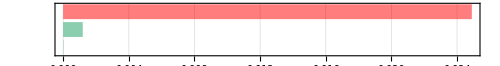
Code | Time, s
NestWhile[Drop[#1,1]&,Range[10000],Length[#1]>10&] | 0.0248999
NestWhile[Drop[#1,1]&,Range[10000 0.9,10000],Length[#1]>10&] | 0.0011913
Drop[Range[10000],10000-10] | 0.0000212
Min Max acceleration is 1174.52 times
-Graphics-

```mathematica
With[{n = 10000, m = 10},
	uCompareTime[{
		NestWhile[Drop[#, 1]&, Range[n], (Length[#]>m)&], 
		NestWhile[Drop[#, 1]&, Range[n 0.9, n], (Length[#]>m)&],
		Drop[Range[n], n - m]
	}]
]
```